{0→0,1→16,2→0,3→0,4→208,5→192,6→144,7→128,8→0,9→0,10→0,11→0,12→16,13→80,14→16,15→0,16→1,17→0,18→0,19→0,20→209,21→192,22→145,23→129,24→1,25→0,26→1,27→0,27→1,28→3,28→19,28→89,29→1,29→3,30→1,31→0,31→1,32→0,33→0,33→16,34→0,35→0,36→208,37→192,37→224,38→144,39→192,40→0,41→0,42→0,43→0,44→0,44→64,44→80,45→137,46→0,47→0,47→128,48→0,48→2,49→0,50→0,50→2,51→32,52→208,53→64,54→144,55→128,56→8,57→0,58→8,59→0,60→8,61→136,62→0,63→8,64→11,65→91,66→11,67→11,68→219,69→235,70→155,71→139,72→11,73→139,74→11,75→3,75→11,76→11,76→27,77→219,78→11,79→11,80→11,81→14,82→11,83→138,84→223,85→234,86→154,87→138,88→10,88→14,88→15,89→10,90→10,90→15,91→10,92→15,93→10,94→27,95→10,96→9,97→25,98→9,99→9,100→217,101→217,102→153,103→136,104→9,105→25,106→9,107→9,108→9,109→137,110→9,111→9,112→8,113→8,114→8,114→12,115→8,116→216,117→200,118→152,119→136,120→8,121→8,122→8,123→8,124→12,125→8,125→24,126→10,127→8,128→0,129→144,130→0,131→128,132→208,133→240,134→144,135→128,136→0,137→0,137→128,138→0,139→0,140→16,141→96,142→16,143→0,144→1,145→0,146→136,147→128,148→216,149→192,150→144,150→145,151→128,152→0,153→0,154→8,155→0,156→0,156→16,156→88,157→64,158→0,158→16,159→0,160→0,161→144,162→0,163→128,164→208,165→240,166→144,167→128,168→0,169→16,170→0,171→0,172→0,173→16,174→16,175→0,176→0,177→16,178→0,179→0,180→144,180→208,181→192,182→144,183→128,184→0,185→0,186→0,187→0,188→0,189→0,190→0,191→0,192→0,193→16,194→128,195→0,195→64,195→128,195→130,196→208,197→193,198→144,199→128,200→0,201→0,202→0,203→0,204→0,204→2,205→113,206→0,207→0,208→6,209→0,209→16,210→2,211→0,211→136,212→209,213→200,213→208,213→224,214→144,215→128,216→10,217→0,218→0,218→8,219→0,220→0,221→0,222→0,223→2,224→0,225→16,226→0,227→128,228→208,229→208,230→144,231→128,232→0,233→16,233→128,234→0,235→0,236→0,237→0,237→1,237→33,238→0,239→64,240→0,241→16,241→128,242→0,243→0,244→208,245→192,246→144,247→128,247→136,248→0,249→0,250→0,251→0,252→0,253→0,254→16,255→0}

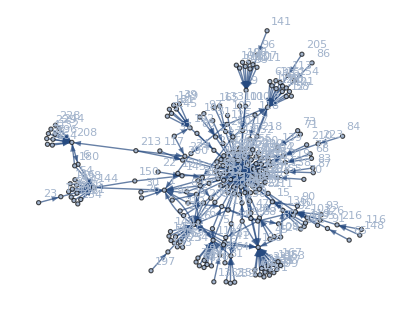

/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/QGraphs/1000.png

```mathematica
weights = Import["/home/lars/Documents/Year 3/Bachelor project/Informatica/new_file.csv"];

edges = {};
Do[Do[If[weights[[i]][[j]]==Max[weights[[i]]],AppendTo[edges,i-1->j-1]],{j,1,256}],{i,1,256}]; 
edges
graph = Graph[edges,ImageSize->Full,VertexLabels->Automatic]

Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/QGraphs/1000.png",graph]
```